```mathematica
(* Solving Friedmann eqn for 3 cases *)
(* Case 1: k=1, lambda=3 (nonzero), rho=0, c=1 *)

(* I'm using simplified version of Friedmann eqn that I worked out on paper beforehand *)
(* Integrating this gives t as a function of a, t=... *)
```

```mathematica
Integrate[(a^2-1)^(-1/2),a]
```

-1/2 Log[1-a/(√(-1+a^2))]+1/2 Log[1+a/(√(-1+a^2))]

```mathematica
(* Like Dr. McGuigan said mathematica gives a weird result for this integral. I used a hyperbolic identity sheet to determine the nicer result of t=arccosh(a) *)
(* Now we can use Solve to invert the nicer result I derived with the identity sheet *)

Solve[t==ArcCosh[a],a]
```

{{a→ConditionalExpression[Cosh[t], (Re[t]>0&&-π<Im[t]≤π)||(Re[t]==0&&0≤Im[t]≤π)]}}

```mathematica
(* Now we can Plot a(t) *)

Plot[Cosh[t],{t,0,10}, BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","a(t)"},PlotPoints->1000,PlotStyle->{Thickness[0.009]}]
```

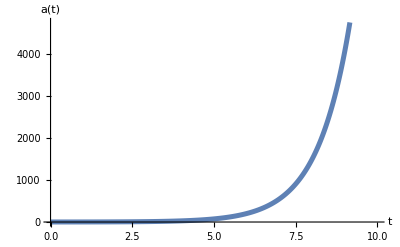

```mathematica
(* This plot shows a(t)=cosh(t) which is what we derived from the integral of the Friedmann eqn where rho=0, k=1, c=1, and lambda=3 *)
(* Ask Dr. McGuigan about the units: can we input time units into cosh? Also how do I deal with the speed of light c, which I set equal to 0 at the beginning? Do I need to incorporate it back in? *)


(* Case 2: k=0, rho=m/a^3 (matter is nonzero, let's use m=1), lambda=0.1 (nonzero) *)
(* Again, I simplified the eqn beforehand on paper so we jump straight to integration *)
(* For now, I'm using 8piG=x just so I can see the result of the integral better *)

G=6.67408*10^(-11)
Integrate[((8*Pi*G/(3*a))+(0.1/3)*a^2),a]
```

6.67408×10^-11

0.0111111 a^3+5.59126×10^-10 Log[a]

```mathematica
(* Use Solve to make equation a(t) *)

Solve[t==0.01111111111111111* a^3+5.59126418599215*10^(-10)*Log[a],a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→(-0.00127991-0.00221687 ⅈ) ProductLog[5.96168×10^7 ⅇ^(5.36551×10^9 t)]^(1/3)},{a→(-0.00127991+0.00221687 ⅈ) ProductLog[5.96168×10^7 ⅇ^(5.36551×10^9 t)]^(1/3)},{a→0.00255983 ProductLog[5.96168×10^7 ⅇ^(5.36551×10^9 t)]^(1/3)}}

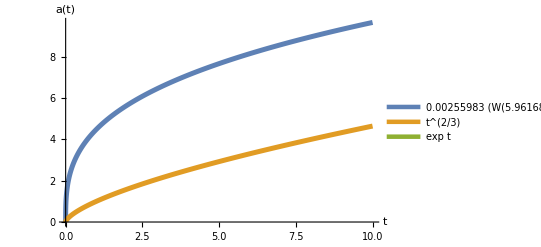

```mathematica
(* Let's Plot the last result for a(t) since the other two don't show up on the graph *)

Plot[{(0.00255983) ProductLog[5.961680*10^7 *ⅇ^(5.365512*10^(9) t)]^(1/3),t^(2/3),exp(t)},{t,0,10},BaseStyle->{FontWeight->"Bold",FontSize->12},AxesLabel->{"t","a(t)"},PlotPoints->1000,PlotStyle->{Thickness[0.009]},PlotLegends->"Expressions"]
```

```mathematica
(* Above is the 3rd solution for a(t) in blue and t^(2/3) in orange which is overlayed exactly with the exp(t) in green. I don't think I want the two reference plots to be overlayed like that so I'll have to come back and fix that next time i'm just out of time rn *)
```